### Инициализация

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;
U0=0.01;
 p0=P0=10000;
b=0.6;a=1;
bx=1;by=1;
Pressure[x_,y_,a_,b_,P0_]=If[(x/a)^2+(y/b)^2≤1,Re[P0 √(1-(x/a)^2-(y/b)^2)],0];
Displacement[x_,y_,a_,b_,U0_]=If[(x/a)^2+(y/b)^2≤1,U0,0];
(*Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,P0,0];*)
s=1.5*a;(*размер расчетной области*)
(*Установить h = 3a/19 для n = 20*)
h= 3a /19;(*размер ГЭ*)
n=2 s/h+1;(*number of elementary units*)
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];

Plot3D[Displacement[x,y,a,b,U0],{x,-s,s},{y,-s,s},PlotRange->All];
```

### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
σ1[x1_,x2_,x3_,a_,b_] =
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]);
```

## 1) Графики

### Графики напряжений

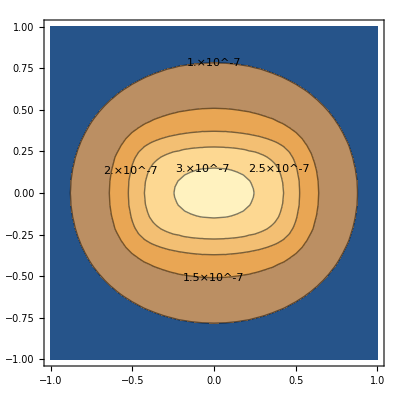

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

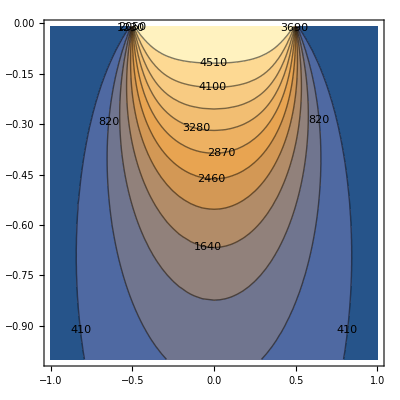

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

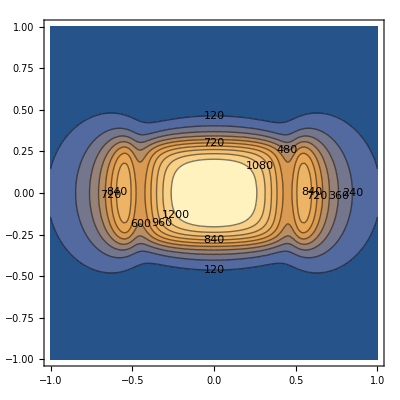

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

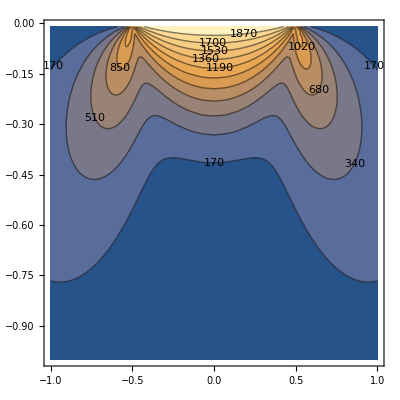

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

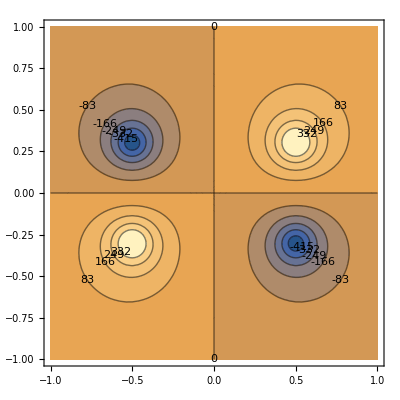

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

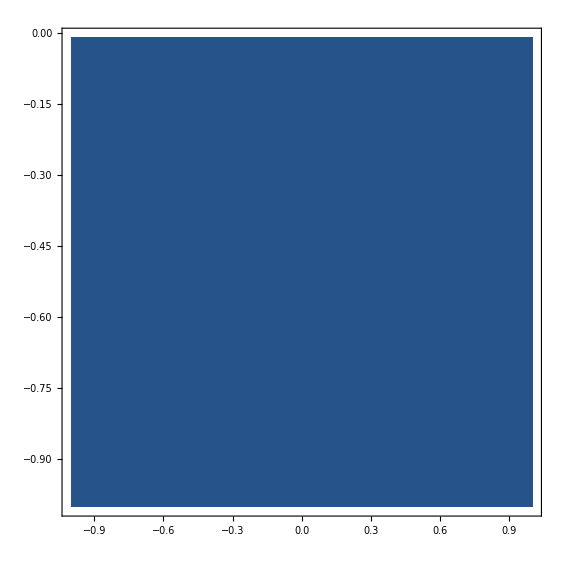

```mathematica
Print[ContourPlot[σ[1,2,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

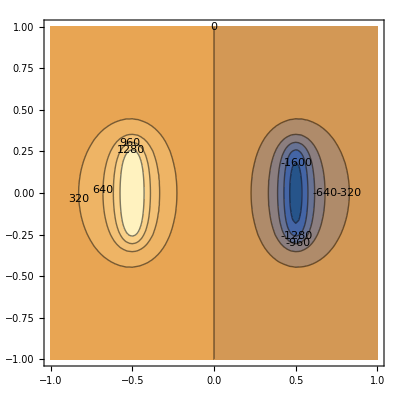

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

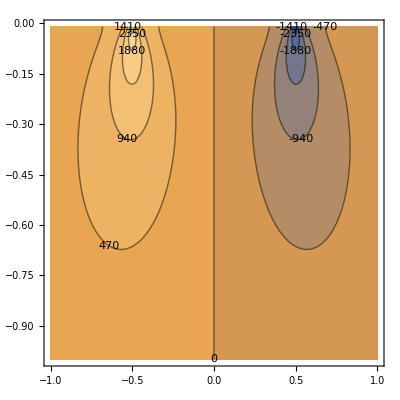

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

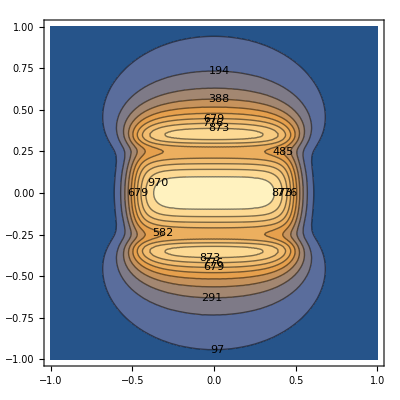

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

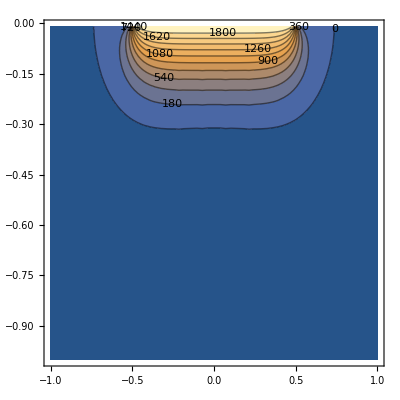

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

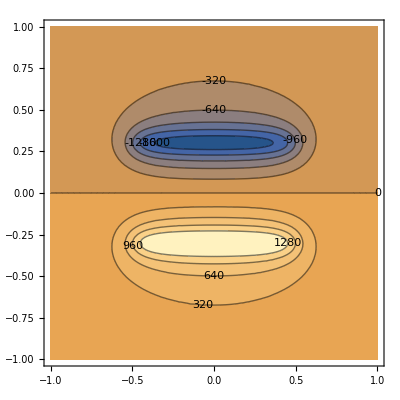

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

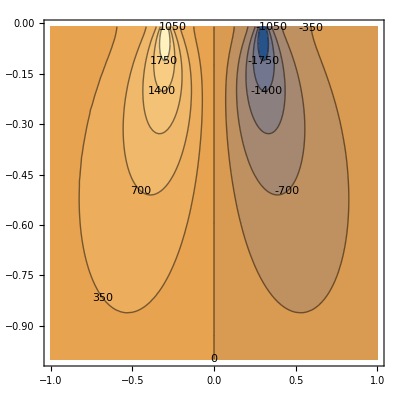

```mathematica
Print[ContourPlot[σ[2,3,3][a/2,a,x+b/2,b,z,P0,λ,μ] ,{x,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

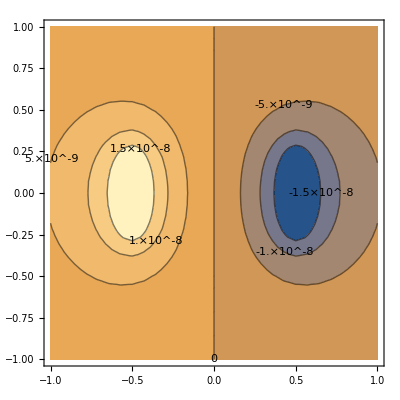

```mathematica
Print[ContourPlot[U[1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

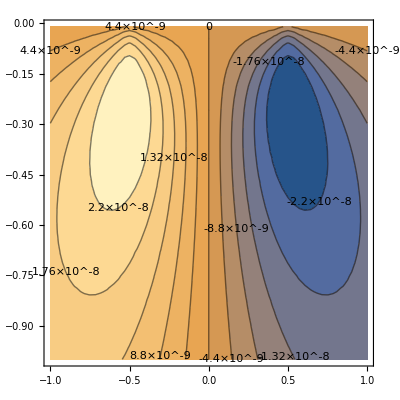

```mathematica
Print[ContourPlot[U[1,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

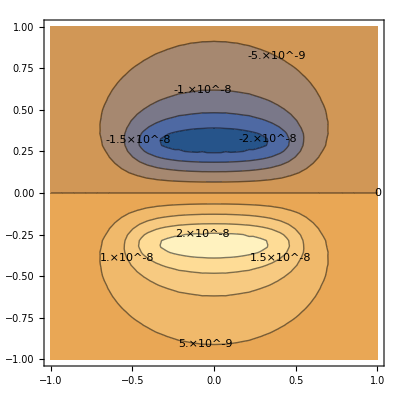

```mathematica
Print[ContourPlot[U[2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

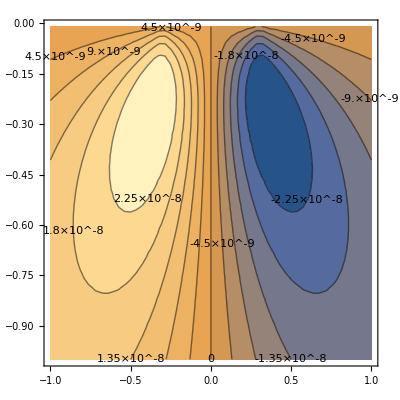

```mathematica
Print[ContourPlot[U[2,3][a/2,a,y+b/2,b,z,P0,λ,μ] ,{y,-by,by},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

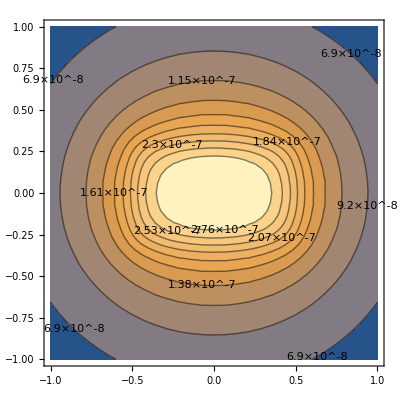

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

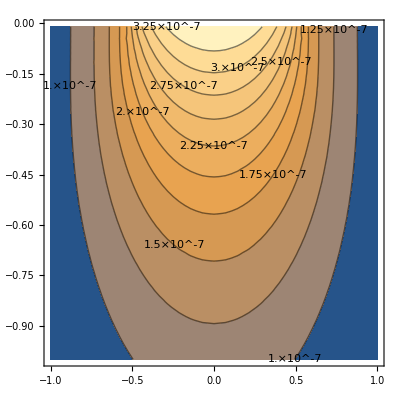

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

## 2) Граничная задача для вдавливания плоского эллиптического штампа

#### Графики функции поверхностного распределения и её дискретизации

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
ListPlot3D[DisplacementTab,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All];
```

```mathematica
BoundaryElements=Table[{X[[xi]],Y[[yj]],DisplacementTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
```

### Получение решения последовательно

```mathematica
PressureSP[xj_,yj_]:=Table[σ[3,3,3][X[[m]]-xj,a,Y[[o]]-yj,b,U0,p0,λ,μ],{m,1,n},{o,1,n}];
```

```mathematica
AbsoluteTiming[Equationq=Flatten[Table[PressureSP[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];]
```

{0.397054,Null}

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
B=FPT=Flatten[DisplacementTab];
Equationq=Flatten[Table[Sum[σ[3,3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,U0,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];
```

```mathematica
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,Filling->Axis,InterpolationOrder->0,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntSRes:=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n σ[3,3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*SolN1q[[i,j]]];
```

```mathematica
Resq=Table[DIntSRes[X[[i]],Y[[j]],U0],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*CUDAQ[] *)
```

```mathematica
(*CUDAResourcesInstall[]*)
```

```mathematica
(*Table[U[3,3][X[[i]]-X[[1]],h,Y[[i]]-Y[[1]],h,0.01,p0,λ,μ],{i,1,n},{j,1,n}]//MatrixForm*)
```

## 3)Перемещения внутри эллипса заданы

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];,
a;
(*Print["i: ",i," j: ",j]*)];

]]
Print["Amount of Boundary elements inside ellipse is: ",amount]
Ak = Table[Subscript[q, k],{k,1,amount}];
DisV[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,U0,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

Amount of Boundary elements inside ellipse is: 76

```mathematica
.
```

```mathematica
Equation2=Table[DisV[X[[Mp[[i,1]]]],Y[[Mp[[i,2]]]]]==U0,{i,1,amount}];
Solq=Solve[Equation2,Ak];
```

```mathematica
SolutionValues=Table[Solq[[1,i,2]],{i,1,amount}];
```

```mathematica
(*добавление столбца со значениями, выполнять только один раз*)
Tmp=Transpose[Mp];
AppendTo[Tmp,SolutionValues];
Mp=Transpose[Tmp];
```

```mathematica
FinalList=Table[0,{i,1,n},{j,1,n}];
```

```mathematica
Table[FinalList[[Mp[[i,1]],Mp[[i,2]]]]=Mp[[i,3]],{i,1,amount}];(*в необходимые места подставляем полученные значения, остальные приравниваем 0, для того, чтобы построить 3-х мерный график*)
```

```mathematica
ListPlot3D[FinalList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntURes[x_,y_,z_]:=If[(x/a)^2+(y/b)^2≤1,∑_(i=1)^n ∑_(j=1)^n U[3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*FinalList[[i,j]],0];
ResU=Table[DIntURes[X[[i]],Y[[j]],U0],{i,1,n},{j,1,n}];
ListPlot3D[ResU,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

## 4) Parallel 2)

```mathematica
AbsoluteTiming[A={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
A=AppendTo[A,Flatten[PressureSP[X[[i]],Y[[j]]]]];]]
]
```

{0.42102,Null}

```mathematica
Ainv=Inverse[A];
```

```mathematica
sf=Dot[B, Ainv];
```

```mathematica
SolN1q = Table[sf[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,U0],{xi,1,n},{yj,1,n}];
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];
(*Print["i: ",i," j: ",j]*)];

]]
Print["Amount of Boundary elements inside ellipse is: ",amount]
Ak = Table[Subscript[q, k],{k,1,amount}];
```

Amount of Boundary elements inside ellipse is: 76

```mathematica
DisV[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,U0,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

```mathematica
Equation2=Table[DisV[X[[Mp[[i,1]]]],Y[[Mp[[i,2]]]]]==U0,{i,1,amount}];
Solq=Solve[Equation2,Ak];
```

```mathematica
SolutionValues=Table[PLS1[[1,i]],{i,1,amount}];
```

```mathematica
(*добавление столбца со значениями, выполнять только один раз*)
Tmp=Transpose[Mp];
AppendTo[Tmp,SolutionValues];
Mp=Transpose[Tmp];
```

```mathematica
FinalList=Table[0,{i,1,n},{j,1,n}];
```

```mathematica
Table[FinalList[[Mp[[i,1]],Mp[[i,2]]]]=Mp[[i,3]],{i,1,amount}];(*в необходимые места подставляем полученные значения, остальные приравниваем 0, для того, чтобы построить 3-х мерный график*)
```

```mathematica
ListPlot3D[FinalList,InterpolationOrder->0,Filling->Axis,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
SolN1q//MatrixForm
```

(-5.14962×10^-8 | 4.80669×10^-8 | -5.18529×10^-8 | 4.78105×10^-8 | -1.52726×10^-7 | 2.397×10^-7 | -3.4372×10^-7 | 4.29596×10^-7 | -7.3155×10^-7 | 1.18658×10^-6 | -1.85438×10^-6 | 2.67027×10^-6 | -4.08913×10^-6 | 6.36432×10^-6 | -9.94538×10^-6 | 0.000015064 | -0.000022954 | 0.0000351664 | -0.0000543996 | 0.0000829874
4.80912×10^-8 | -4.5001×10^-8 | 4.8389×10^-8 | -4.47614×10^-8 | 1.42642×10^-7 | -2.24257×10^-7 | 3.21398×10^-7 | -4.01796×10^-7 | 6.83962×10^-7 | -1.11031×10^-6 | 1.7344×10^-6 | -2.49932×10^-6 | 3.825×10^-6 | -5.9573×10^-6 | 9.30694×10^-6 | -0.0000141035 | 0.0000214853 | -0.0000329321 | 0.0000509183 | -0.0000777907
-5.18562×10^-8 | 4.83555×10^-8 | -5.21928×10^-8 | 4.81141×10^-8 | -1.53746×10^-7 | 2.41504×10^-7 | -3.45764×10^-7 | 4.33337×10^-7 | -7.35881×10^-7 | 1.19535×10^-6 | -1.86763×10^-6 | 2.69026×10^-6 | -4.12007×10^-6 | 6.41135×10^-6 | -0.0000100205 | 0.0000151802 | -0.0000231328 | 0.000035446 | -0.0000548228 | 0.0000836848
4.78209×10^-8 | -4.47821×10^-8 | 4.8126×10^-8 | -4.45154×10^-8 | 1.41947×10^-7 | -2.22744×10^-7 | 3.20813×10^-7 | -3.95872×10^-7 | 6.90961×10^-7 | -1.11096×10^-6 | 1.734×10^-6 | -2.49019×10^-6 | 3.82041×10^-6 | -5.97151×10^-6 | 9.32939×10^-6 | -0.0000141189 | 0.000021508 | -0.0000330056 | 0.0000511041 | -0.0000781689
-5.21254×10^-8 | 4.85703×10^-8 | -5.24585×10^-8 | 4.83563×10^-8 | -1.54415×10^-7 | 2.43279×10^-7 | -3.43924×10^-7 | 4.54139×10^-7 | -8.96236×10^-6 | 9.43326×10^-6 | -0.0000101012 | 0.0000109599 | -0.0000202899 | 0.0000383297 | -0.000057708 | 0.0000787103 | -0.000117982 | 0.000192112 | -0.000303392 | 0.000454554
4.75215×10^-8 | -4.45515×10^-8 | 4.78285×10^-8 | -4.42706×10^-8 | 1.41133×10^-7 | -2.20937×10^-7 | 3.28305×10^-7 | -8.61974×10^-6 | 0.0000253111 | -0.0000257501 | 0.0000263859 | -0.0000431978 | 0.0000759079 | -0.000116945 | 0.000167423 | -0.000250739 | 0.000397297 | -0.000622633 | 0.000945152 | -0.00142522
-5.3272×10^-8 | 4.95703×10^-8 | -5.36018×10^-8 | 4.937×10^-8 | -1.58175×10^-7 | 2.49216×10^-7 | -3.64162×10^-7 | 8.67659×10^-6 | -0.0000254149 | 0.000025906 | -0.0000266174 | 0.0000435482 | -0.0000764821 | 0.00011784 | -0.000168824 | 0.000252865 | -0.000400667 | 0.000627873 | -0.000953341 | 0.00143837
-5.2918×10^-8 | 4.92231×10^-8 | -5.3402×10^-8 | 4.90256×10^-8 | -1.55189×10^-7 | 2.45007×10^-7 | -3.31676×10^-7 | -7.81771×10^-6 | 0.0000239334 | -0.0000234957 | 0.0000228672 | -0.0000382039 | 0.0000683077 | -0.000105095 | 0.000148896 | -0.000222867 | 0.00035509 | -0.000558279 | 0.000845326 | -0.00127581
1.41686×10^-7 | -1.32843×10^-7 | 1.42723×10^-7 | -1.32067×10^-7 | 4.1873×10^-7 | -6.44593×10^-7 | -7.28605×10^-6 | 0.0000234793 | -0.000039095 | 0.0000379002 | -0.0000521821 | 0.0000978102 | -0.000156852 | 0.000212973 | -0.000305295 | 0.00049453 | -0.000797313 | 0.00120752 | -0.0017963 | 0.00274689
-2.49053×10^-7 | 2.32453×10^-7 | -2.50969×10^-7 | 2.31132×10^-7 | -7.35841×10^-7 | 1.14311×10^-6 | 6.58219×10^-6 | -0.0000226124 | 0.0000375969 | -0.0000354655 | 0.0000483897 | -0.0000924117 | 0.000148588 | -0.000200093 | 0.000285147 | -0.000464206 | 0.000751238 | -0.00113716 | 0.00168708 | -0.00258249
3.36778×10^-7 | -3.1538×10^-7 | 3.39098×10^-7 | -3.13826×10^-7 | 9.94797×10^-7 | -1.55207×10^-6 | -5.99868×10^-6 | 0.0000218823 | -0.0000364708 | 0.0000335682 | -0.0000453758 | 0.0000880113 | -0.000141981 | 0.00018996 | -0.000269364 | 0.000440146 | -0.000714714 | 0.00108166 | -0.00160187 | 0.00245261
-4.45123×10^-7 | 4.15605×10^-7 | -4.48501×10^-7 | 4.13087×10^-7 | -1.31632×10^-6 | 2.04849×10^-6 | 5.27608×10^-6 | -0.0000210545 | 0.0000190444 | -0.0000151806 | 0.0000255832 | -0.0000667468 | 0.00010291 | -0.000116183 | 0.000158175 | -0.000288906 | 0.000488991 | -0.000715124 | 0.00102418 | -0.00158884
5.31854×10^-7 | -4.9792×10^-7 | 5.35483×10^-7 | -4.95556×10^-7 | 1.57075×10^-6 | -2.46613×10^-6 | 3.53639×10^-6 | -0.0000122434 | 0.0000469741 | -0.0000516895 | 0.0000584787 | -0.0000817909 | 0.0001404 | -0.000229764 | 0.000340063 | -0.000494793 | 0.000761778 | -0.00119772 | 0.00184373 | -0.00276837
-6.4435×10^-7 | 6.01685×10^-7 | -6.49121×10^-7 | 5.98183×10^-7 | -1.90663×10^-6 | 2.98286×10^-6 | -4.32459×10^-6 | 0.0000293724 | -0.0000969913 | 0.000102734 | -0.000111077 | 0.000167635 | -0.000290595 | 0.00046058 | -0.000670761 | 0.000989985 | -0.00154525 | 0.002423 | -0.00370151 | 0.00556788
5.35705×10^-7 | -5.01528×10^-7 | 5.38983×10^-7 | -4.99111×10^-7 | 1.58773×10^-6 | -2.49312×10^-6 | 3.5212×10^-6 | -0.0000444533 | 0.000143671 | -0.000148578 | 0.000155323 | -0.00024115 | 0.000421787 | -0.000662523 | 0.00095635 | -0.00141615 | 0.0022222 | -0.00348581 | 0.00530814 | -0.0079847
-2.659×10^-7 | 2.47259×10^-7 | -2.67399×10^-7 | 2.45759×10^-7 | -7.94789×10^-7 | 1.2791×10^-6 | -0.0000179407 | 0.0000988741 | -0.000237027 | 0.000239729 | -0.000274643 | 0.000465719 | -0.000785082 | 0.0011584 | -0.00166421 | 0.00255568 | -0.00405862 | 0.00627047 | -0.00944904 | 0.0142945
-2.26966×10^-7 | 2.12045×10^-7 | -2.29945×10^-7 | 2.10312×10^-7 | -6.58116×10^-7 | 9.53244×10^-7 | 0.0000308668 | -0.000143314 | 0.000319045 | -0.000317673 | 0.000377846 | -0.000654895 | 0.00109129 | -0.00158035 | 0.00226721 | -0.0035226 | 0.00561249 | -0.00863236 | 0.0129646 | -0.0196566
8.79014×10^-7 | -8.24327×10^-7 | 8.86689×10^-7 | -8.19866×10^-7 | 2.57684×10^-6 | -3.93355×10^-6 | -0.0000427527 | 0.000186376 | -0.000391119 | 0.000384227 | -0.000467733 | 0.000828115 | -0.00137022 | 0.00195365 | -0.00279689 | 0.00438597 | -0.00701173 | 0.0107468 | -0.016096 | 0.0244391
-1.7575×10^-6 | 1.6436×10^-6 | -1.77224×10^-6 | 1.63411×10^-6 | -5.16591×10^-6 | 7.94243×10^-6 | 0.0000532594 | -0.000228261 | 0.000429584 | -0.0004152 | 0.000519403 | -0.000961558 | 0.0015762 | -0.002188 | 0.00311654 | -0.00496724 | 0.0079928 | -0.0121853 | 0.0181582 | -0.0276416
2.78104×10^-6 | -2.60611×10^-6 | 2.80522×10^-6 | -2.5915×10^-6 | 8.181×10^-6 | -0.0000126405 | -0.0000464411 | 0.000204409 | -0.00033826 | 0.000314956 | -0.000406207 | 0.000803194 | -0.00130532 | 0.00174617 | -0.00246397 | 0.0040177 | -0.0065335 | 0.00989432 | -0.0146446 | 0.0223647)